## Expression:

```mathematica
3 + x + x^2
```

3+x+x^2

```mathematica
{1, 2, 3}
```

{1,2,3}

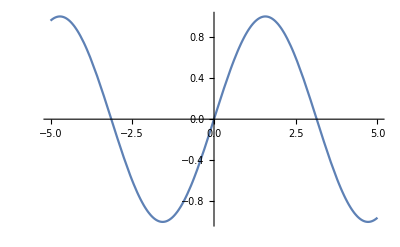

```mathematica
Plot[Sin[x], {x, -5, 5}]
```

```mathematica
?FullForm
```

FullForm[expr] prints as the full form of expr, with no special syntax.

```mathematica
FullForm[3+x]
```

Plus[3,x]

```mathematica
FullForm[2+x+x^2]
```

Plus[2,x,Power[x,2]]

```mathematica
expr = 3+x
```

3+x

```mathematica
?FullForm
```

FullForm[expr] prints as the full form of expr, with no special syntax.

```mathematica
?Head
```

Head[expr] gives the head of expr.

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.
expr[[key]] gives the value associated with the key "key" in an association expr.
expr[[Key[k]]] gives the value associated with an arbitrary key k in the association expr.

```mathematica
FullForm[expr]
```

Plus[3,x]

```mathematica
Head[expr]
```

Plus

```mathematica
Part[expr]
```

3+x

```mathematica
Part[expr, 0]
```

Plus

```mathematica
expr[[1]]
```

3

```mathematica
expr[[0]]
```

Plus

```mathematica
f[x, y]
```

f[x,y]

```mathematica
FullForm[{1, 2, 3}]
```

List[1,2,3]

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,{1}] or f@@@expr replaces heads at level 1 of expr by f.
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec. 
Apply[f] represents an operator form of Apply that can be applied to an expression.

```mathematica
Apply[List, expr]
```

{3,x}

```mathematica
Apply[Plus, {1, 2, 3}]
```

6

```mathematica
List@@expr
```

{3,x}

```mathematica
Plus@@{1, 2,3}
```

```mathematica
6
```

6

```mathematica
Pi
```

π

```mathematica
DMSList[N[π/°]]
```